# SKS Initial conditions

## Import metric

```mathematica
Import["~/llgsks.mx"]
```

## Initial data elipse

```mathematica
ClearAll[elipseID];
elipseID[BHParams_,InitPos_,LocalEnergy_,ParticleMass_,param_]:=Module[
{llg,En,m,LEPUM,velNorm,AA,BB,CC,DD,FF,GG,Δ,J,II,α,β,X0,Y0,θ},

llg=llgSKS//.Ω->√((M1+M2)/b^3);
llg=llg//.{
M1->BHParams⟦1⟧,
M2->BHParams⟦2⟧,

a1->BHParams⟦3⟧,
a2->BHParams⟦4⟧,

b->BHParams⟦5⟧,

t->0,
x->InitPos⟦1⟧,
y->InitPos⟦2⟧,
z->0
};

En=LocalEnergy;
m=ParticleMass;

LEPUM=En/m;
velNorm=1-(1/LEPUM)^2;

AA=llg⟦2,2⟧;
BB=llg⟦2,3⟧;
CC=llg⟦3,3⟧;
DD=0;
FF=0;
GG=-velNorm;

Δ=Det[{{AA,BB,DD},{BB,CC,FF},{DD,FF,GG}}];
J=Det[{{AA,BB},{BB,CC}}];
II=AA+CC;

If[!(Δ≠0&&J>0&&Δ/II<0),
Print["Unphysical configuration"];
Abort[];
];

X0=(CC*DD-BB*FF)/(BB^2-AA*CC);
Y0=(AA*FF-BB*DD)/(BB^2-AA*CC);

α=√((2(AA*FF^2+CC*DD^2+GG*BB^2-2*BB*DD*FF-AA*CC*GG))/((BB^2-AA*CC)(√((AA-CC)^2+4*BB^2)-(AA+CC))));
β=√((2(AA*FF^2+CC*DD^2+GG*BB^2-2*BB*DD*FF-AA*CC*GG))/((BB^2-AA*CC)(-√((AA-CC)^2+4*BB^2)-(AA+CC))));

θ=Piecewise[
{
{0,BB==0&&AA<CC},
{π/2,BB==0&&AA>CC},
{ArcCot[(AA-CC)/(2BB)]/2,BB≠0&&AA<CC},
{π/2+ArcCot[(AA-CC)/(2BB)]/2,BB≠0&&AA>CC}
}
];

Return[{X0+α Cos[param] Cos[θ]-β Sin[param] Sin[θ],Y0+β Cos[θ] Sin[param]+α Cos[param] Sin[θ]}];
]
```

## Single trajectory

Vx = 0.5414790691374123
Vy = -0.3617918046876465
x0 = 11.
b = 20.

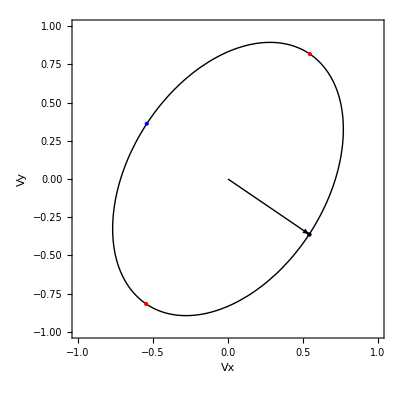

```mathematica
Block[
{M1,M2,a1,a2,b,x0,y0,En,m,X0,Y0,α,β,θ,curve,pt},
M1=1/2;
M2=1/2;

a1=98/100M1;
a2=98/100M2;

b=20;

x0=b/2+1;
y0=0;

En=1*10^(0);
m=10^(-1);

curve=elipseID[{M1,M2,a1,a2,b},{x0,y0},En,m,param];
pt=curve//.param->-100/200*π;

Print["Vx = ",N[pt⟦1⟧,16],"\nVy = ",N[pt⟦2⟧,16],"\nx0 = ",N[x0,16],"\nb = ",N[b,16]];

ParametricPlot[
curve,
{param,0,2π},

PlotRange->{{-1,1},{-1,1}},
PlotStyle->Directive[Black,Thick],

Axes->False,
Frame->True,

FrameLabel->{"Vx","Vy"},

Epilog->{
PointSize[Large],
Red,
Point[curve//.param->0],
Point[curve//.param->π],

Blue,
Point[curve//.param->π/2],
Point[curve//.param->3π/2],

Black,
Arrow[{{0,0},pt}],
Point[pt]
}
]
]
```

## Penrose distance sweep

```mathematica
Block[
{M1,M2,a1,a2,b0,bf,bCount,δb,bi,x0,y0,En1,m1,En2,m2,param1,param2,pt1,pt2},
M1=1/2;
M2=1/2;

a1=98/100M1;
a2=98/100M2;

b0=10;
bf=69/10;
bCount=10;
δb=Abs[(bf-b0)]/bCount;

Do[
bi=b0-i*δb;

x0=bi/2+13/10;
y0=0;

En1=1;
m1=1/10;
param1=-25/200*π;

En2=8*10^-3;
m2=10^-4;
param2=-100/200*π;

pt1=elipseID[{M1,M2,a1,a2,bi},{x0,y0},En1,m1,param1];
pt2=elipseID[{M1,M2,a1,a2,bi},{x0,y0},En2,m2,param2];

Print[
"b = ",N[bi,16],
"\nx0 = ",N[x0,16],

"\nVx1 = ",N[pt1⟦1⟧,16],
"\nVy1 = ",N[pt1⟦2⟧,16],

"\nVx2 = ",N[pt2⟦1⟧,16],
"\nVy2 = ",N[pt2⟦2⟧,16],
"\n-------------------------"
];
,
{i,0,bCount-1}
];
]
```

b = 10.
x0 = 6.3
Vx1 = 0.6598181850110646
Vy1 = 0.6757023252679782
Vx2 = 0.6229320417788412
Vy2 = -0.3287115744960509
-------------------------

b = 9.69
x0 = 6.145
Vx1 = 0.6600372787690648
Vy1 = 0.6747216707336837
Vx2 = 0.6219959776044865
Vy2 = -0.3290193500753698
-------------------------

b = 9.38
x0 = 5.99
Vx1 = 0.6602552575267571
Vy1 = 0.6736908149354469
Vx2 = 0.6210154613385279
Vy2 = -0.3293346639676775
-------------------------

b = 9.07
x0 = 5.835
Vx1 = 0.6604716830270784
Vy1 = 0.6726050523314579
Vx2 = 0.6199867626956065
Vy2 = -0.3296580760119002
-------------------------

b = 8.76
x0 = 5.68
Vx1 = 0.6606860643479333
Vy1 = 0.6714590267660181
Vx2 = 0.6189056878671335
Vy2 = -0.3299902402647783
-------------------------

b = 8.45
x0 = 5.525
Vx1 = 0.6608978534615584
Vy1 = 0.6702466115887511
Vx2 = 0.6177675015094857
Vy2 = -0.3303319276791845
-------------------------

b = 8.14
x0 = 5.37
Vx1 = 0.6611064411953404
Vy1 = 0.6689607619293215
Vx2 = 0.6165668318762518
Vy2 = -0.3306840553384208
-------------------------

b = 7.83
x0 = 5.215
Vx1 = 0.6613111540916025
Vy1 = 0.6675933312454501
Vx2 = 0.6152975545799888
Vy2 = -0.3310477244321803
-------------------------

b = 7.52
x0 = 5.06
Vx1 = 0.6615112529435897
Vy1 = 0.6661348416019507
Vx2 = 0.6139526490059731
Vy2 = -0.3314242699918046
-------------------------

b = 7.21
x0 = 4.905
Vx1 = 0.6617059342116439
Vy1 = 0.6645741934244523
Vx2 = 0.6125240193736668
Vy2 = -0.3318153265945586
-------------------------

## Penrose M2 sweep

```mathematica
Block[
{M1,M2initial,M2final,M2count,δM2,a1,b,x0,y0,En1,m1,param1,En2,m2,param2,pt1,pt2,M2i,a2i},
M1=1/2;

M2initial=1/2;
M2final=1/4;
M2count=10;
δM2=Abs[M2initial-M2final]/M2count;

a1=98/100M1;

b=20;

x0=b/2+1;
y0=0;

En1=1;
m1=1/10;
param1=-25/200*π;

En2=8*10^-3;
m2=10^-4;
param2=-100/200*π;

Do[
M2i=M2initial-i*δM2;
a2i=98/100*M2i;

En1=1;
m1=1/10;
param1=-25/200*π;

En2=8*10^-3;
m2=10^-4;
param2=-100/200*π;

pt1=elipseID[{M1,M2i,a1,a2i,b},{x0,y0},En1,m1,param1];
pt2=elipseID[{M1,M2i,a1,a2i,b},{x0,y0},En2,m2,param2];

Print[
"M2 = ",N[M2i,16],
"\na2 = ",N[a2i,16],

"\nVx1 = ",N[pt1⟦1⟧,16],
"\nVy1 = ",N[pt1⟦2⟧,16],

"\nVx2 = ",N[pt2⟦1⟧,16],
"\nVy2 = ",N[pt2⟦2⟧,16],
"\n-------------------------"
];
,
{i,0,M2count-1}
];
]
```

M2 = 0.5
a2 = 0.49
Vx1 = 0.7136437091380091
Vy1 = 0.618219567436815
Vx2 = 0.5457169635641801
Vy2 = -0.3646233739211139
-------------------------

M2 = 0.475
a2 = 0.4655
Vx1 = 0.7138735413650489
Vy1 = 0.6186944679787532
Vx2 = 0.5462318075181109
Vy2 = -0.3647413085165727
-------------------------

M2 = 0.45
a2 = 0.441
Vx1 = 0.7140958900665264
Vy1 = 0.6191774618437871
Vx2 = 0.5467552062657255
Vy2 = -0.3648541312251246
-------------------------

M2 = 0.425
a2 = 0.4165
Vx1 = 0.714310355203082
Vy1 = 0.6196688945196138
Vx2 = 0.5472875284935116
Vy2 = -0.3649615684005971
-------------------------

M2 = 0.4
a2 = 0.392
Vx1 = 0.7145165094774592
Vy1 = 0.6201691364630963
Vx2 = 0.5478291676871514
Vy2 = -0.3650633266731968
-------------------------

M2 = 0.375
a2 = 0.3675
Vx1 = 0.7147138956741288
Vy1 = 0.6206785856258763
Vx2 = 0.5483805445354626
Vy2 = -0.3651590909635618
-------------------------

M2 = 0.35
a2 = 0.343
Vx1 = 0.7149020236549162
Vy1 = 0.6211976703119921
Vx2 = 0.5489421096433583
Vy2 = -0.365248522236123
-------------------------

M2 = 0.325
a2 = 0.3185
Vx1 = 0.7150803669546121
Vy1 = 0.621726852422039
Vx2 = 0.5495143466039146
Vy2 = -0.3653312549489707
-------------------------

M2 = 0.3
a2 = 0.294
Vx1 = 0.7152483589094325
Vy1 = 0.6222666311492916
Vx2 = 0.5500977754895458
Vy2 = -0.3654068941488847
-------------------------

M2 = 0.275
a2 = 0.2695
Vx1 = 0.7154053882374532
Vy1 = 0.6228175472066673
Vx2 = 0.5506929568345214
Vy2 = -0.3654750121496257
-------------------------